```mathematica
$LoadFeynArts=True;
<<FeynCalc`
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

args::shdw: Symbol args appears in multiple contexts {FeynArts`,Global`}; definitions in context FeynArts` may shadow or be shadowed by other definitions.

FeynArts 3.9 patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

```mathematica
$FAVerbose=0;
```

```mathematica
$Path
```

{/Applications/Mathematica.app/Contents/AddOns/Applications,/Users/shibayasushi/Library/Mathematica/DocumentationIndices,/Applications/Mathematica.app/Contents/SystemFiles/Links,/Users/shibayasushi/Library/Mathematica/Kernel,/Users/shibayasushi/Library/Mathematica/Autoload,/Users/shibayasushi/Library/Mathematica/Applications,/Library/Mathematica/Kernel,/Library/Mathematica/Autoload,/Library/Mathematica/Applications,.,/Users/shibayasushi,/Applications/Mathematica.app/Contents/AddOns/Packages,/Applications/Mathematica.app/Contents/SystemFiles/Autoload,/Applications/Mathematica.app/Contents/AddOns/Autoload,/Applications/Mathematica.app/Contents/AddOns/Applications,/Applications/Mathematica.app/Contents/AddOns/ExtraPackages,/Applications/Mathematica.app/Contents/SystemFiles/Kernel/Packages,/Applications/Mathematica.app/Contents/Documentation/English/System,/Applications/Mathematica.app/Contents/SystemFiles/Data/ICC}

```mathematica
SystemOpen["/Users/shibayasushi/Library/Mathematica/"]
```

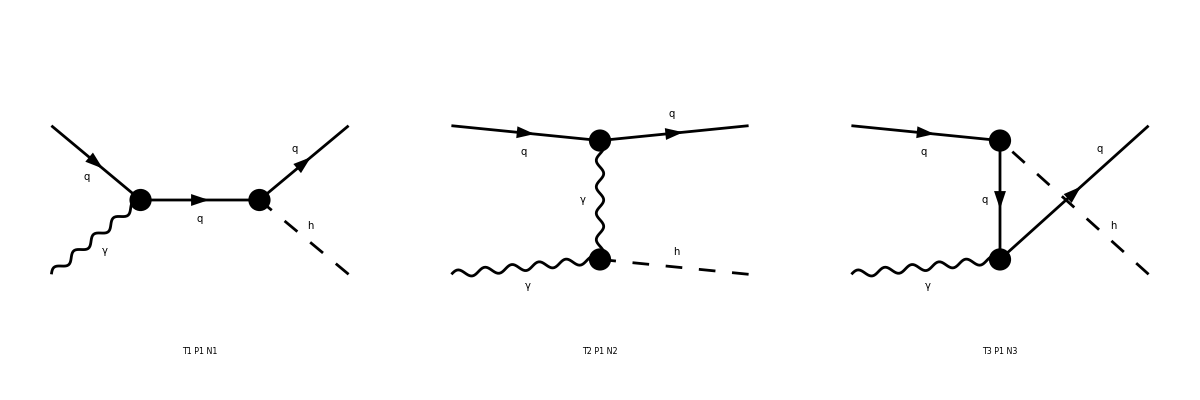

FeynArtsGraphics({q,\gamma}→{q,h})(([T1 P1 N1] | [T2 P1 N2] | [T3 P1 N3]
Null | Null | Null
Null | Null | Null))

```mathematica
diags=InsertFields[CreateTopologies[0,2->2],{F[2],V[1]}->{F[2],S[1]},InsertionLevel->{Particles},Model->{"bbg"},GenericModel->{"Lorentz_1"}];
Paint[diags]
```

```mathematica
amp=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p[1],p[2]},OutgoingMomenta->{p[3],p[4]}]/.{GS->gs,a->yb Cos[α],b->yb Sin[α],c->gs^2/12/Pi/v};
```

```mathematica
amp
```

{1/((-p(3)-p(4))^2-MB^2)(ε̄)^Lor1(p(2)) (φ(OverBar[p(3)],MB)).((γ̄)^7 (-yb sin(α)-ⅈ yb cos(α))+(γ̄)^6 (yb sin(α)-ⅈ yb cos(α))).(γ̄·(OverBar[p(3)]+OverBar[p(4)])+MB).(ⅈ gs (γ̄)^Lor1.(γ̄)^6+ⅈ gs (γ̄)^Lor1.(γ̄)^7).(φ(OverBar[p(1)],MB)),-1/(p(4)-p(2))^2(ḡ)^Lor2Lor3 (ε̄)^Lor1(p(2)) (φ(OverBar[p(3)],MB)).(ⅈ gs (γ̄)^Lor2.(γ̄)^6+ⅈ gs (γ̄)^Lor2.(γ̄)^7).(φ(OverBar[p(1)],MB)) ((ⅈ gs^2 (ḡ)^Lor1Lor3 (OverBar[p(2)]·(OverBar[p(4)]-OverBar[p(2)])))/(3 π v)-(ⅈ gs^2 (OverBar[p(4)]-OverBar[p(2)])^Lor1 OverBar[p(2)]^Lor3)/(3 π v)),1/((p(2)-p(3))^2-MB^2)(ε̄)^Lor1(p(2)) (φ(OverBar[p(3)],MB)).(ⅈ gs (γ̄)^Lor1.(γ̄)^6+ⅈ gs (γ̄)^Lor1.(γ̄)^7).(γ̄·(OverBar[p(3)]-OverBar[p(2)])+MB).((γ̄)^7 (-yb sin(α)-ⅈ yb cos(α))+(γ̄)^6 (yb sin(α)-ⅈ yb cos(α))).(φ(OverBar[p(1)],MB))}

```mathematica
SetMandelstam[s,t,u,p[1],p[2],-p[3],-p[4],0,0,0,MH^2];
tmp=Plus@@amp;
ampS=(ComplexConjugate[tmp]/.{Lor1->Lor4,Lor2->Lor5,Lor3->Lor6}) tmp//DoPolarizationSums[#,p[2],0]&//FermionSpinSum//TR//Contract//Simplify;
```

```mathematica
ampS
```

4/9 gs^2 ((gs^4 (1/(p(4)-p(2))^2)^2 (MH^4-t) (MH^4 (-(s-t+u))+s^2-t^2+u^2))/(π^2 v^2)+(2 gs^4 MH^4 (1/(p(4)-p(2))^2)^2 s u)/(π^2 v^2)-(gs^4 (1/(p(4)-p(2))^2)^2 t (MH^4-t)^2)/(π^2 v^2)-(72 yb^2 (MH^4-s) (s+t))/((p(2)-p(3))^2 (-p(3)-p(4))^2)-36 (1/(-p(3)-p(4))^2)^2 yb^2 (MH^8-MH^4 (s+t+u)+s u)-36 (1/(p(2)-p(3))^2)^2 s u yb^2)

```mathematica
cs=1/16/Pi/s^2 ampS//PropagatorDenominatorExplicit//ReplaceAll[#,{MB->0,u->MH^2-s-t}]&//Simplify;
```

(gs^2 yb^2 (MH^10-MH^8 (s+t+1)+MH^6 (s+t)+MH^4 s (2 s+2 t+1)-2 MH^2 s (s+t)+s t^2))/(π s^4 (-MH^2+s+t))-(gs^6 (MH^10-MH^8 (t+1)+MH^6 t+MH^4 t-2 MH^2 t (s+t)+t (2 s^2+2 s t+t^2)))/(36 π^3 s^2 t^2 v^2)

```mathematica
csAngular=cs/.{t->(s-MH^2)/2 (Sin[th]-1)}//FullSimplify;
```

```mathematica
csAngular
```

1/(72 π^3 s^4)gs^2 (1/(v^2 (MH^2-s)^2 (sin(th)-1)^2)gs^4 s^2 (-4 MH^10-4 MH^8 (s-1)+MH^6 (4 s-1)+3 MH^4 s-7 MH^2 s^2+(MH^2-s) sin(th) ((MH^2-s)^2 sin(th) (sin(th)+1)+2 MH^2 s-(1-2 MH^2)^2 MH^4+3 s^2)+5 s^3)+36 π^2 yb^2 (-2 MH^8+2 MH^6+4 MH^4 s+s (s-MH^2) sin(th)-MH^2 s+(4 s (2 MH^6-2 MH^2 s+s^2))/((s-MH^2) (sin(th)+1))-3 s^2))

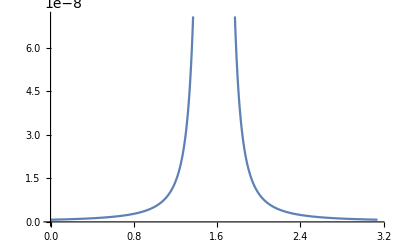

```mathematica
Plot[-csAngular/.{MH->125,v->174,s->1300^2,gs->1,yb->4.7/174},{th,0,Pi}]
```